```mathematica
(* Related to the Quora question: How can you fold a square to make a square of one-fifth the area of the original square https://www.quora.com/How-can-you-fold-a-square-to-make-a-square-of-one-fifth-the-area-of-the-original-squareNonehttps://www.quora.com/How-can-you-fold-a-square-to-make-a-square-of-one-fifth-the-area-of-the-original-squareHyperlinkActionRecycledHyperlinkActive*)
```

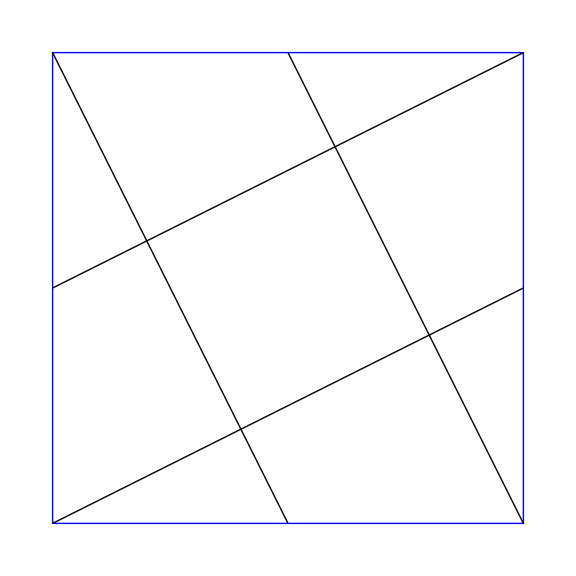

```mathematica
Graphics[{{Blue,Line[{{0,0}, {0,1}, {1,1}, {1,0},{0,0}}]}, Line[{{{0,0}, {1,1/2}},{{0,1/2}, {1,1}},{{0,1}, {1/2,0}}, {{1/2,1}, {1,0}}}]}, {ImageSize->Large, GridLines->{{0,1/2,1}, {0,1/2,1}}}]
```

```mathematica
l1[x_]:= 1/2x
l2[x_]:=-2x+1
l3[x_]:=-2(x-1)
```

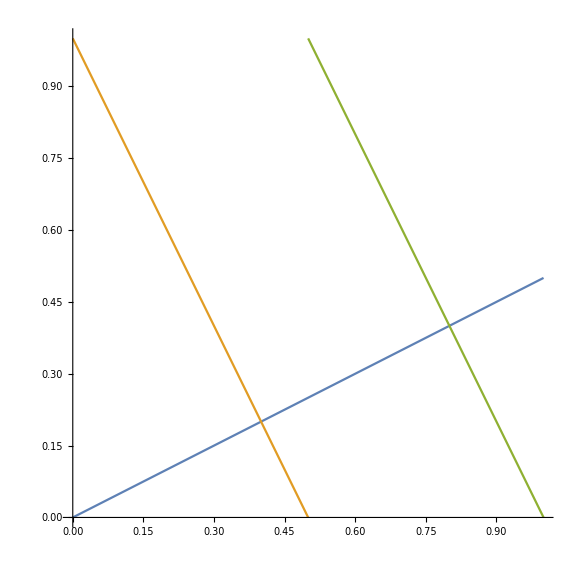

```mathematica
Plot[{l1[x], l2[x], l3[x]}, {x, 0, 1}, {AspectRatio->1, PlotRange->{{0,1}, {0,1}}, ImageSize->Large, GridLines->{{0,1/2,1}, {0,1/2,1}}}]
```

```mathematica
p1x=x/.Solve[l1[x]==l2[x], x]⟦1⟧
```

2/5

```mathematica
p2x=x/.Solve[l1[x]==l3[x], x]⟦1⟧
```

4/5

```mathematica
p1y=l1[p1x]
```

1/5

```mathematica
p2y=l1[p2x]
```

2/5

```mathematica
p1={p1x, p1y}
p2={p2x, p2y}
```

{2/5,1/5}

{4/5,2/5}

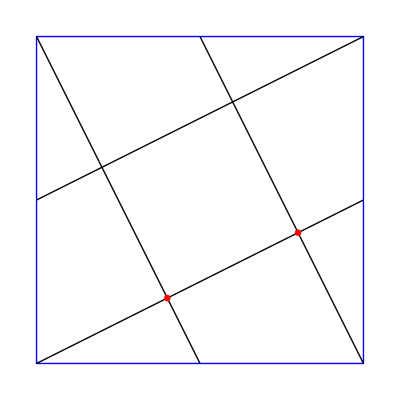

```mathematica
Graphics[{{Blue,Line[{{0,0}, {0,1}, {1,1}, {1,0},{0,0}}]}, Line[{{{0,0}, {1,1/2}},{{0,1/2}, {1,1}},{{0,1}, {1/2,0}}, {{1/2,1}, {1,0}}}], {Red, {Disk[p1,1/100], Disk[p2,1/100]}}}]
```

```mathematica
Norm[p2-p1]^2
```

1/5

```mathematica
(* A reasonable way to obtain the angle θ to fold the sides of a square sheet (always through one of the corners, for simplicity) in order to obtain an area 𝒜 would be: *)
(* Write the equation of the line ℓ1 that passes through {0, 0} (square's lower left corner) with slope corresponding to θ: *)
Subscript[l1, θ_][x_]:= Tan[θ]x
```

```mathematica
(* Write the equation of the perpendicular (justified because of the square requirements) line ℓ2 that passes through {0, 1} (square's upper left corner) in terms of θ: *)
Subscript[l2, θ_][x_]:= Tan[θ+π/2]x+1
```

```mathematica
(* Write the equation of the perpendicular (justified because of the square requirements) line ℓ3 that passes through {1, 0} (square's lower right corner) in terms of θ: *)
Subscript[l3, θ_][x_]:= Tan[θ+π/2](x-1)
```

```mathematica
Subscript[l4, θ_][x_]:= Tan[θ](x-1)+1
```

```mathematica
Manipulate[Plot[{Subscript[l1, θ][x], Subscript[l2, θ][x], Subscript[l3, θ][x], Subscript[l4, θ][x]}, {x, 0, 1},{Evaluated-> True, AspectRatio->1, PlotRange->{{0,1}, {0,1}},ImageSize->Large}], {θ, ArcTan[0], ArcTan[1]}]
```

```mathematica
(* Compute the intersection points of ℓ1 and ℓ2, and of ℓ1 and ℓ3 in terms of θ: *)
p1x=x/.(Solve[Subscript[l1, θ][x]==Subscript[l2, θ][x], x]//Flatten)//FullSimplify
```

Cos[θ] Sin[θ]

```mathematica
p2x=x/.(Solve[Subscript[l1, θ][x]==Subscript[l3, θ][x], x]//Flatten)//FullSimplify
```

Cos[θ]^2

```mathematica
p1y=Subscript[l1, θ][p1x]//FullSimplify
```

Sin[θ]^2

```mathematica
p2y=Subscript[l1, θ][p2x]//FullSimplify
```

Cos[θ] Sin[θ]

```mathematica
p1={p1x, p1y}
p2={p2x, p2y}
```

{Cos[θ] Sin[θ],Sin[θ]^2}

{Cos[θ]^2,Cos[θ] Sin[θ]}

```mathematica
(* Solve for the desired square area 𝒜 in terms of θ: *)
Solve[Norm[p2-p1]^2==𝒜, θ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{θ→-ArcCos[-(√(1-√(-((-2+𝒜) 𝒜))))/(√2)]},{θ→ArcCos[-(√(1-√(-((-2+𝒜) 𝒜))))/(√2)]},{θ→-ArcCos[(√(1-√(-((-2+𝒜) 𝒜))))/(√2)]},{θ→ArcCos[(√(1-√(-((-2+𝒜) 𝒜))))/(√2)]},{θ→-ArcCos[-(√(1+√(-((-2+𝒜) 𝒜))))/(√2)]},{θ→ArcCos[-(√(1+√(-((-2+𝒜) 𝒜))))/(√2)]},{θ→-ArcCos[(√(1+√(-((-2+𝒜) 𝒜))))/(√2)]},{θ→ArcCos[(√(1+√(-((-2+𝒜) 𝒜))))/(√2)]}}

```mathematica
(* Compute the value of θ for 𝒜=1/5: *)
θ[𝒜_]:= ArcTan[(1-𝒜)/(1+√(2 𝒜-𝒜^2))]
θ[1/5]
```

ArcTan[1/2]

```mathematica
(* Show it working: *)
Manipulate[Column[{Show[Plot[{Subscript[l1, θ][x], Subscript[l2, θ][x], Subscript[l3, θ][x], Subscript[l4, θ][x]}, {x, 0, 1},{Evaluated->True, AspectRatio->1, PlotRange->{{0,1}, {0,1}},ImageSize->Large}], Graphics[{Red, {Disk[p1, 1/200],Disk[p2, 1/200]}, {Blue,{Disk[{1,Subscript[l1, θ][1]},1/200],Dashed,Line[{{0,Subscript[l1, θ][1]},{1,Subscript[l1, θ][1]}} ]}}}]],Row[{"𝒜: ",Norm[p1-p2]^2}], Row[{"side: ", Subscript[l1, θ][1]}]}/.Symbol["θ"]-> θ], {θ, 10^-3, π/4}]
```

```mathematica
(* Export it (remember to disable dynamic updating): *)
```

```mathematica
frames={};
Animate[(AppendTo[frames,Column[{Show[Plot[{Subscript[l1, θ][x], Subscript[l2, θ][x], Subscript[l3, θ][x], Subscript[l4, θ][x]}, {x, 0, 1},{Evaluated->True, AspectRatio->1, PlotRange->{{0,1}, {0,1}},ImageSize->Large}], Graphics[{Red, {Disk[p1, 1/200],Disk[p2, 1/200]}, {Blue,{Disk[{1,Subscript[l1, θ][1]},1/200],Dashed,Line[{{0,Subscript[l1, θ][1]},{1,Subscript[l1, θ][1]}} ]}}}]],Row[{"𝒜: ",Norm[p1-p2]^2}], Row[{"side: ", Subscript[l1, θ][1]}]}/.Symbol["θ"]-> θ]])⟦-1⟧, {θ, 0, π/4}, AnimationRepetitions->1]
```

```mathematica
Length[frames]
```

369

```mathematica
base=DirectoryName[NotebookFileName[]];
```

```mathematica
Export[base<>"/SquareFolding.gif", Join[{frames⟦1⟧},frames⟦9;;108⟧]]
```

/Users/mauro/Projects/Mathematica//SquareFolding.gif